# Algebraic structures of the Lindblad equation

Leonel Bixano
Centro de Investigación y de Estudios Avanzados del Instituto Politécnico Nacional,
Departamento de Física,

Guillermo López-Alvarez,  Victor Alberto Cruz-Barriguete, Victor Guadalupe Ibarra-Sierra, José Luis Cardoso, Juan Carlos Sandoval-Santana, Alejandro Kunold
Área de Física Teórica y Materia Condensada
Universidad Autónoma Metropolitana

## Abstract

This  Mathematica notebook accompanies the paper The Algebraic Structure of the Lindblad Equation. The notebook illustrates the proposed algebraic formulation through the example of a driven transmon qubit described by the Lindblad master equation.

The example is organized as a step-by-step implementation of the algebraic method. It begins by constructing the Hermitian matrix basis and the associated algebraic objects, followed by the recursive generation of the operators required to represent the Liouville superoperator. The model-dependent quantities are then assembled to obtain the complete Liouville superoperator, which is compared with the one obtained by the conventional direct construction, demonstrating their exact agreement.

The notebook is fully parameterized with respect to the number of qubits, allowing the same implementation to be extended to larger Hilbert spaces. Although some symbolic calculations become computationally demanding as the system size increases, the code provides a general framework that can be readily adapted to study a broad class of finite-dimensional open quantum systems.

## Licence

LindbladAlgebra Mathematica examples accompanying the paper

“The Algebraic Structure of the Lindblad Equation”

Copyright (c) 2026 Alejandro Kunold and collaborators

This notebook is distributed under the MIT License. Permission is hereby granted, free of charge, to any person obtaining a copy of this software and associated documentation files (the “Software”), to deal in the Software without restriction, including without limitation the rights to use, copy, modify, merge, publish, distribute, sublicense, and/or sell copies of the Software, subject to the conditions of the MIT License.

A copy of the full license is available in the LICENSE file of this repository.

In this section we create a series of Mathematica functions that facilitate the computation of the matrix basis, structure constants and Liouville superoperator.

## Functions

In this section we create a series of Mathematica functions that facilitate the computation of the matrix basis, structure constants and Liouville superoperator.

### Functions

```mathematica
NQubitBasis[nq_]:=Module[{h0,h1,sq2},
sq2=1/√2.0;
h0=SparseArray[{{1,1,1}->sq2,{1,2,2}->sq2,{2,1,2}->sq2,{2,2,1}->sq2,{3,1,2}->-ⅈ sq2,{3,2,1}->ⅈ sq2,{4,1,1}->sq2,{4,2,2}->-sq2}];
h1=h0;
Do[
h1=KroneckerProduct[h1,h0];
,{ii,nq-1}];
h1
]

QubitBasis[nq_]:=Module[{h0,h1},
h0=SparseArray[{{1,1,1}->1/(√2),{1,2,2}->1/(√2),{2,1,2}->1/(√2),{2,2,1}->1/(√2),{3,1,2}->-ⅈ/(√2),{3,2,1}->ⅈ/(√2),{4,1,1}->1/(√2),{4,2,2}->-1/(√2)}];
h1=h0;
Do[
h1=KroneckerProduct[h1,h0];
,{ii,nq-1}];
h1
]

NStateBasis[nl_]:=Module[{sq2,vb,v,ars,splist,kk},
sq2=1/√2;
vb={ConstantArray[1,nl]};
Do[
v=ConstantArray[0,nl];
v[[ii]]=1;
AppendTo[vb,v];
,{ii,nl,2,-1}];
ars=ArrayRules[SparseArray[Map[DiagonalMatrix,Orthogonalize[vb]]]];
splist=ars[[;;Length[ars]-1]];
kk=nl;
Do[
kk+=1;
AppendTo[splist,{kk,ii,jj}->sq2];
AppendTo[splist,{kk,jj,ii}->sq2];
kk+=1;
AppendTo[splist,{kk,ii,jj}->-ⅈ sq2];
AppendTo[splist,{kk,jj,ii}->ⅈ sq2];
,{ii,1,nl-1},{jj,ii+1,nl}];
SparseArray[splist,{nl^2,nl,nl}]
]

BCStructureConstantsFromBase[h_]:=Module[{hs,hhh,hhht},
hhh=TensorContract[h.Transpose[h].Transpose[h],{{2,5}}];
hhht=Transpose[hhh];
{SparseArray[hhh+hhht],SparseArray[ⅈ (hhht-hhh)]}]

BCStructureConstantsFromQubits[nq_]:=Module[{h0,c0,b0,c1,b1,c2,b2},
h0=QubitBasis[1];
{b0,c0}=BCStructureConstantsFromBase[h0];
b1=b0;
c1=c0;
Do[
b2=1/2(KroneckerProduct[b1,b0]-KroneckerProduct[c1,c0]);
c2=1/2(KroneckerProduct[c1,b0]+KroneckerProduct[b1,c0]);
b1=b2;
c1=c2;
,{ii,nq-1}];
{b1,c1}]

ZStructureConstantFromBase[h_]:=SparseArray[2TensorContract[h.Transpose[h].Transpose[h],{{2,5}}]]

ZStructureConstantsFromQubits[nq_]:=Module[{b0,c0,z0,z1,c1,b1,c2,b2},
{b0,c0}=BCStructureConstantsFromBase[QubitBasis[1]];
z0=b0+ⅈ c0;
z1=z0;
Do[
z1=1/2 KroneckerProduct[z1,z0];
,{ii,nq-1}];
z1]

NZStructureConstantsFromQubits[nq_]:=Module[{b0,c0,z0,z1,c1,b1,c2,b2},
{b0,c0}=BCStructureConstantsFromBase[NQubitBasis[1]];
z0=b0+ⅈ c0;
z1=z0;
Do[
z1=1/2 KroneckerProduct[z1,z0];
,{ii,nq-1}];
z1]

XBasisFromZ[Z_]:=1/4 Transpose[Z.ConjugateTranspose[Z],{1,3,2,4}]

XBasisFromBC[b_,c_]:=1/4 Transpose[(b+ⅈ c).Transpose[b-ⅈ c],{1,3,2,4}]

XBasisFromQubits[nq_]:=Module[{b,c},
{b,c}=BCStructureConstantsFromQubits[nq];
1/4 Transpose[(b+ⅈ c).Transpose[b-ⅈ c],{1,3,2,4}]]

LambdaFromHamiltonianLindbladian[Z_,H_,Γ_]:=Module[{n,trGZ},
n=Length[H];
trGZ=TensorContract[Transpose[Γ].Z,{{1,2}}];
(Γ+n^(1/4)(KroneckerProduct[SparseArray[{1->1},n],(ⅈ H-1/4 trGZ)]+-KroneckerProduct[(ⅈ H+1/4 trGZ),SparseArray[{1->1},n]]))
]

GammaFromgamma[h_,γ_,A_,At_]:=Module[{w,wt},
w=TensorContract[A.Transpose[h],{{2,4}}];
wt = TensorContract[h.Transpose[At],{{2,4}}];
wt.γ.w
]

LiouvilleSOFromProjection[h_,H_,Γ_]:=Module[{hhh,trhhh,trhhhhG,tc24trhhhhG,tc14trhhhhG},
hhh=h.Transpose[h].Transpose[h];
trhhh=SparseArray[TensorContract[hhh,{{2,5}}]];
trhhhhG=TensorContract[hhh.Transpose[h],{{2,6}}].Γ;
tc24trhhhhG=TensorContract[trhhhhG,{{2,4}}];
tc14trhhhhG=TensorContract[trhhhhG,{{1,4}}];
-ⅈ H.(trhhh-Transpose[trhhh,{1,3,2}])+tc24trhhhhG-1/2 tc14trhhhhG-1/2 Transpose[tc14trhhhhG]
]

LiouvilleSOFromLamda[X_,Λ_]:=TensorContract[Transpose[Λ].X,{{1,2}}]

ProjectOperatorOntoBasis[op_,h_]:=TensorContract[h.op,{{2,3}}]
```

## Example 1. One qubit.

### One-qubit matrix basis h

In the following example we verify the main relations derived in the paper for the one qubit case.

```mathematica
nq=1;
```

We begin by constructing the one-qubit basis 𝔥_n and its associated structure constant superoperators Z, Z^* and X.

```mathematica
h=QubitBasis[nq];
{b,c}=BCStructureConstantsFromQubits[nq];
z=ZStructureConstantsFromQubits[nq];
zt=Conjugate[z];
x=XBasisFromQubits[nq];
```

The  complex structure-constant superoperators can be visualized with the following line of code.

```mathematica
MatrixForm[z[[3]]]
```

(0 | 0 | √2 | 0
0 | 0 | 0 | -ⅈ √2
√2 | 0 | 0 | 0
0 | ⅈ √2 | 0 | 0)

It can be verified that Z and Z^* constitute to independent realizations of the Lie algebra associated with h by showing that the following difference, obtained by subtracting the right-hand side from the left-hand side of Eqs. (69) and (70), vanish identically.

```mathematica
zz=Transpose[z.Transpose[z],{1,3,2,4}];
commu=SparseArray[zz-Transpose[zz]];
PossibleZeroQ[SparseArray[commu+2ⅈ c.z]]
```

SparseArray[…]

```mathematica
ztzt=Transpose[zt.Transpose[zt],{1,3,2,4}];
commu=SparseArray[ztzt-Transpose[ztzt]];
PossibleZeroQ[SparseArray[commu-2ⅈ c.zt]]
```

SparseArray[…]

Similarly we can verify that Z, Z^* commute.

```mathematica
zzt=Transpose[z.ConjugateTranspose[z]];
ztz=Transpose[zt.Transpose[z],{3,1,2,4}];
commu=SparseArray[zzt-ztz];
PossibleZeroQ[commu]
```

SparseArray[…]

The structure of the 16 elements of X can be visualized using the following line of code.

```mathematica
MatrixForm[x[[2,3]]]
```

(0 | 0 | 0 | ⅈ/2
0 | 0 | 1/2 | 0
0 | 1/2 | 0 | 0
-ⅈ/2 | 0 | 0 | 0)

The Lie and Jordan algebraic relations of X can be verified by evaluating the following differences, obtained by subtracting the right-hand side from the left-hand side of Eqs. (81) and (82), and verifying that they vanish identically.  This calculation may exceed the available memory if n_q⩾2.

```mathematica
xx=Transpose[x.Transpose[x,{2,3,1,4}],{1,2,5,3,4,6}];
commu=SparseArray[xx-Transpose[xx,{3,4,1,2,5,6}]];
anticommu=SparseArray[xx+Transpose[xx,{3,4,1,2,5,6}]];
```

```mathematica
PossibleZeroQ[SparseArray[commu-1/4 Transpose[(zt.Transpose[x,{1,4,2,3}].z-z.Transpose[x,{1,4,2,3}].zt),{1,3,5,6,2,4}]]]
```

SparseArray[…]

```mathematica
PossibleZeroQ[SparseArray[anticommu-1/4 Transpose[(zt.Transpose[x,{1,4,2,3}].z+z.Transpose[x,{1,4,2,3}].zt),{1,3,5,6,2,4}]]]
```

SparseArray[…]

The orthonormality of 𝔛_(n^2) is verified by flattening the first two indices of X into a single index and then evaluating the Hilbert-Schmidt inner product

```mathematica
X=Flatten[x,1]
```

SparseArray[…]

```mathematica
XX=SparseArray[TensorContract[X.Transpose[X],{{2,4}}]]
DiagonalMatrixQ[XX]
```

SparseArray[…]

True

### Hamiltonian

A convenient system for illustrating the results developed in this work is the transmon qubit. Since the number of quantum levels retained in the model can be chosen arbitrarily, it provides a simple framework for studying the behavior of the algebraic structures introduced above as the Hilbert-space dimension increases. We first define the lowering and rasing operators as well as the jump operators

```mathematica
m=2^nq;
n=2^(2nq);
a=SparseArray[Table[{n+1,n+2}->√(n+1),{n,0,m-2}],m];
at=SparseArray[Table[{n+1,n}->√n,{n,1,m-1}],m];
A=SparseArray[Table[{n+1,n+1,n+2}->√(n+1),{n,0,m-2}],{m-1,m,m}];
At=SparseArray[Table[{n+1,n+2,n+1}->√(n+1),{n,0,m-2}],{m-1,m,m}];
```

The Hamiltonian in the interaction picture, given by Eq. (122) is given by

```mathematica
ψ = Exp[-ⅈ (Δ t +ϕ)]Map[Exp,ⅈ α t (1-Range[m-1])];
ψt=Exp[ⅈ (Δ t +ϕ)]Map[Exp,-ⅈ α t (1-Range[m-1])];
Hi=Ω/2(ψ.A+ψt.At);
Hi//MatrixForm
```

(0 | 1/2 ⅇ^(-ⅈ (t Δ+ϕ)) Ω
1/2 ⅇ^(ⅈ (t Δ+ϕ)) Ω | 0)

The Hamiltonian vector is obtained by projecting the Hamiltonian on the elements of the set 𝔥_n through Eq. (23).

```mathematica
H=ExpToTrig[ProjectOperatorOntoBasis[Hi,h]];
MatrixForm[H]
```

(0
(Ω Cos[t Δ+ϕ])/(√2)
(Ω Sin[t Δ+ϕ])/(√2)
0)

### Lindbladian

To construct the Lindbladian, we first introduce the corresponding jump operators. In the case of transmons, two decoherence processes are particularly relevant: energy relaxation and pure dephasing. Energy relaxation describes the loss of an excitation from the transmon to its environment and is represented by the Lindblad jump operator J_1=a. This process is characterized by the relaxation time T_1, time or equivalently by the relaxation rate  Γ_1=1/T_1.  Although the corresponding contribution to the Lindbladian is time independent in the Schrödinger picture, it becomes time dependent in the interaction picture used here to express the Hamiltonian. For a harmonic oscillator a simple scalar phase cancels completely, but for the anharmonic transmon the phase contains the number operator n=a^†a, that introduces the time dependency. This time dependency is easily introduced through the phases and decomposing into transition operators the lowering and rising operators

```mathematica
J1=SparseArray[Table[{n,n,n+1}->√n Exp[-ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
J1t=SparseArray[Table[{n,n+1,n}->√n Exp[ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
```

The Lindbladian corresponding to the energy relaxation part is defined by Eq. (38)

```mathematica
γ1=SparseArray[Flatten[Table[{ii,jj}->γ10,{ii,m-1},{jj,m-1}]],{m-1,m-1}];
Γ1=GammaFromgamma[h,γ1,J1,J1t];
MatrixForm[Γ1]
```

(0 | 0 | 0 | 0
0 | γ10/2 | (ⅈ γ10)/2 | 0
0 | -(ⅈ γ10)/2 | γ10/2 | 0
0 | 0 | 0 | 0)

Pure dephasing describes a phenomenon that does not change the energy-level populations but instead, destroys coherence between different energy eigenstates. It is characterized by the jump operator J_2=a^†a

```mathematica
J2 = SparseArray[{at.a}];
J2t = SparseArray[{at.a}];
```

and the pure-dephasing time T_2 or rate Γ_2=1/T_1-1/2 T_2  which is associated

```mathematica
γ2=SparseArray[{{γ20}}];
Γ2=GammaFromgamma[h,γ2,J2,J2t];
MatrixForm[Γ2]
```

(γ20/2 | 0 | 0 | -γ20/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-γ20/2 | 0 | 0 | γ20/2)

The full Lindbladian is therefore

```mathematica
Γ=Γ1+Γ2;
MatrixForm[Γ]
```

(γ20/2 | 0 | 0 | -γ20/2
0 | γ10/2 | (ⅈ γ10)/2 | 0
0 | -(ⅈ γ10)/2 | γ10/2 | 0
-γ20/2 | 0 | 0 | γ20/2)

### Algebraic Method

Having obtained the quantities required to construct the Hamiltonian and Lindbladian contributions to the Liouville superoperator, namely H and Γ, we can proceed to compute Λ using Eq. (60), yielding

```mathematica
Λ=LambdaFromHamiltonianLindbladian[z,H,Γ]
MatrixForm[Λ]
```

SparseArray[…]

(γ20/2+(-√2 γ10-√2 γ20)/(√2) | ⅈ Ω Cos[t Δ+ϕ] | ⅈ Ω Sin[t Δ+ϕ] | -γ20/2+(√2 γ10+√2 γ20)/(2 √2)
-ⅈ Ω Cos[t Δ+ϕ] | γ10/2 | (ⅈ γ10)/2 | 0
-ⅈ Ω Sin[t Δ+ϕ] | -(ⅈ γ10)/2 | γ10/2 | 0
-γ20/2+(√2 γ10+√2 γ20)/(2 √2) | 0 | 0 | γ20/2)

The Liouville superoperator is obtained using Eq. (59).

```mathematica
Lam=SparseArray[LiouvilleSOFromLamda[x,Λ]]
MatrixForm[Lam]
```

SparseArray[…]

(γ10/2+γ20/4+1/2 (γ20/2+(-√2 γ10-√2 γ20)/(√2)) | 0 | 0 | -γ10/2-γ20/2+(√2 γ10+√2 γ20)/(2 √2)
0 | -γ20/4+1/2 (γ20/2+(-√2 γ10-√2 γ20)/(√2)) | 0 | -Ω Sin[t Δ+ϕ]
0 | 0 | -γ20/4+1/2 (γ20/2+(-√2 γ10-√2 γ20)/(√2)) | Ω Cos[t Δ+ϕ]
γ10/2-γ20/2+(√2 γ10+√2 γ20)/(2 √2) | Ω Sin[t Δ+ϕ] | -Ω Cos[t Δ+ϕ] | -γ10/2+γ20/4+1/2 (γ20/2+(-√2 γ10-√2 γ20)/(√2)))

### Direct method

The Liouville superoperator is also computed in the same matrix basis for comparison. The two methods are found to yield identical results.

```mathematica
Ldm=SparseArray[LiouvilleSOFromProjection[h,H,Γ]]
MatrixForm[Ldm]
```

SparseArray[…]

(0 | 0 | 0 | 0
0 | -γ10/2-γ20/2 | 1/2 (-(ⅈ γ10)/2-(ⅈ γ20)/2)+1/2 ((ⅈ γ10)/2+(ⅈ γ20)/2) | -Ω Sin[t Δ+ϕ]
0 | 1/2 (-(ⅈ γ10)/2-(ⅈ γ20)/2)+1/2 ((ⅈ γ10)/2+(ⅈ γ20)/2) | -γ10/2-γ20/2 | Ω Cos[t Δ+ϕ]
γ10 | Ω Sin[t Δ+ϕ] | -Ω Cos[t Δ+ϕ] | -γ10)

### Comparison of the algebraic method and the direct method

To compare the Liouville superoperators obtained using the algebraic and direct methods, we subtract one superoperator from the other.

```mathematica
PossibleZeroQ[SparseArray[Lam-Ldm]]
```

SparseArray[…]

### Liouville equation for the dynamical map

To verify that the dynamical differential equations for the coordinate vector, Eq. (112), are equivalent to those derived from the Lindbladian, we directly project the Liouville operator acting on the dynamical map, as given on the right-hand side of Eq. (110), onto the basis X. We then subtract the resulting expression from the right-hand side of Eq. (112), which should yield zero if both formulations are equivalent. First, we define the elements of the dynamical map as in Eq. (107).

```mathematica
V=SparseArray[Array[v[##][t]&,{n,n}]];
```

We calculate the right-hand side of the dynamical differential equations using the algebraically derived Eq. (112).

```mathematica
DiffEqsAlgebraicMethod=SparseArray[Flatten[V].Flatten[Transpose[SparseArray[1/4 zt.Λ.z],{1,3,2,4}],1]]
```

SparseArray[…]

Here, we project the Liouville operator obtained through the direct method, acting on the dynamical map as given on the right-hand side of Eq. (110), onto the basis X.

```mathematica
DiffEqsDirectMethod=TensorContract[Transpose[V].TensorContract[x.Transpose[x,{2,3,1,4}].Ldm,{{3,6}}],{{1,2}}]
```

SparseArray[…]

Finally, we compare the results obtained by both methods.

```mathematica
PossibleZeroQ[SparseArray[DiffEqsDirectMethod-DiffEqsAlgebraicMethod]]
```

SparseArray[…]

## Example 2. Two qubits.

### Two-qubit matrix basis h

In the following example we verify the main relations derived in the paper for the two qubit case.

```mathematica
nq=2;
```

We begin by constructing the two-qubit basis 𝔥_n and its associated structure constant superoperators Z, Z^* and X.

```mathematica
h=QubitBasis[nq];
{b,c}=BCStructureConstantsFromQubits[nq];
z=ZStructureConstantsFromQubits[nq];
zt=Conjugate[z];
x=XBasisFromQubits[nq];
```

The  complex structure-constant superoperators can be visualized with the following line of code.

```mathematica
MatrixForm[z[[3]]]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0)

It can be verified that Z and Z^* constitute to independent realizations of the Lie algebra associated with h by showing that the following difference, obtained by subtracting the right-hand side from the left-hand side of Eqs. (69) and (70), vanish identically.

```mathematica
zz=Transpose[z.Transpose[z],{1,3,2,4}];
commu=SparseArray[zz-Transpose[zz]];
PossibleZeroQ[SparseArray[commu+2ⅈ c.z]]
```

SparseArray[…]

```mathematica
ztzt=Transpose[zt.Transpose[zt],{1,3,2,4}];
commu=SparseArray[ztzt-Transpose[ztzt]];
PossibleZeroQ[SparseArray[commu-2ⅈ c.zt]]
```

SparseArray[…]

Similarly we can verify that Z, Z^* commute.

```mathematica
zzt=Transpose[z.ConjugateTranspose[z]];
ztz=Transpose[zt.Transpose[z],{3,1,2,4}];
commu=SparseArray[zzt-ztz];
PossibleZeroQ[commu]
```

SparseArray[…]

The structure of the 16 elements of X can be visualized using the following line of code.

```mathematica
MatrixForm[x[[2,3]]]
```

(0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/4 | 0 | 0 | 0)

The Lie and Jordan algebraic relations of X can be verified by evaluating the following differences, obtained by subtracting the right-hand side from the left-hand side of Eqs. (81) and (82), and verifying that they vanish identically.  This calculation may exceed the available memory if n_q⩾2.

```mathematica
xx=Transpose[x.Transpose[x,{2,3,1,4}],{1,2,5,3,4,6}];
commu=SparseArray[xx-Transpose[xx,{3,4,1,2,5,6}]];
anticommu=SparseArray[xx+Transpose[xx,{3,4,1,2,5,6}]];
```

```mathematica
PossibleZeroQ[SparseArray[commu-1/4 Transpose[(zt.Transpose[x,{1,4,2,3}].z-z.Transpose[x,{1,4,2,3}].zt),{1,3,5,6,2,4}]]]
```

SparseArray[…]

```mathematica
PossibleZeroQ[SparseArray[anticommu-1/4 Transpose[(zt.Transpose[x,{1,4,2,3}].z+z.Transpose[x,{1,4,2,3}].zt),{1,3,5,6,2,4}]]]
```

SparseArray[…]

The orthonormality of 𝔛_(n^2) is verified by flattening the first two indices of X into a single index and then evaluating the Hilbert-Schmidt inner product

```mathematica
X=Flatten[x,1]
```

SparseArray[…]

```mathematica
XX=SparseArray[TensorContract[X.Transpose[X],{{2,4}}]]
DiagonalMatrixQ[XX]
```

SparseArray[…]

True

### Hamiltonian

A convenient system for illustrating the results developed in this work is the transmon qubit. Since the number of quantum levels retained in the model can be chosen arbitrarily, it provides a simple framework for studying the behavior of the algebraic structures introduced above as the Hilbert-space dimension increases. We first define the lowering and rasing operators as well as the jump operators

```mathematica
m=2^nq;
n=2^(2nq);
a=SparseArray[Table[{n+1,n+2}->√(n+1),{n,0,m-2}],m];
at=SparseArray[Table[{n+1,n}->√n,{n,1,m-1}],m];
A=SparseArray[Table[{n+1,n+1,n+2}->√(n+1),{n,0,m-2}],{m-1,m,m}];
At=SparseArray[Table[{n+1,n+2,n+1}->√(n+1),{n,0,m-2}],{m-1,m,m}];
```

The Hamiltonian in the interaction picture, given by Eq. (122) is given by

```mathematica
ψ = Exp[-ⅈ (Δ t +ϕ)]Map[Exp,ⅈ α t (1-Range[m-1])];
ψt=Exp[ⅈ (Δ t +ϕ)]Map[Exp,-ⅈ α t (1-Range[m-1])];
Hi=Ω/2(ψ.A+ψt.At);
Hi//MatrixForm
```

(0 | 1/2 ⅇ^(-ⅈ (t Δ+ϕ)) Ω | 0 | 0
1/2 ⅇ^(ⅈ (t Δ+ϕ)) Ω | 0 | (ⅇ^(-ⅈ t α-ⅈ (t Δ+ϕ)) Ω)/(√2) | 0
0 | (ⅇ^(ⅈ t α+ⅈ (t Δ+ϕ)) Ω)/(√2) | 0 | 1/2 √3 ⅇ^(-2 ⅈ t α-ⅈ (t Δ+ϕ)) Ω
0 | 0 | 1/2 √3 ⅇ^(2 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0)

The Hamiltonian vector is obtained by projecting the Hamiltonian on the elements of the set 𝔥_n through Eq. (23).

```mathematica
H=ExpToTrig[ProjectOperatorOntoBasis[Hi,h]];
MatrixForm[H]
```

(0
1/2 Ω Cos[t Δ+ϕ]+1/2 √3 Ω Cos[2 t α+t Δ+ϕ]
1/2 Ω Sin[t Δ+ϕ]+1/2 √3 Ω Sin[2 t α+t Δ+ϕ]
0
0
(Ω Cos[t α+t Δ+ϕ])/(√2)
-(Ω Sin[t α+t Δ+ϕ])/(√2)
0
0
(Ω Sin[t α+t Δ+ϕ])/(√2)
(Ω Cos[t α+t Δ+ϕ])/(√2)
0
0
1/2 Ω Cos[t Δ+ϕ]-1/2 √3 Ω Cos[2 t α+t Δ+ϕ]
1/2 Ω Sin[t Δ+ϕ]-1/2 √3 Ω Sin[2 t α+t Δ+ϕ]
0)

### Lindbladian

To construct the Lindbladian, we first introduce the corresponding jump operators. In the case of transmons, two decoherence processes are particularly relevant: energy relaxation and pure dephasing. Energy relaxation describes the loss of an excitation from the transmon to its environment and is represented by the Lindblad jump operator J_1=a. This process is characterized by the relaxation time T_1, time or equivalently by the relaxation rate  Γ_1=1/T_1.  Although the corresponding contribution to the Lindbladian is time independent in the Schrödinger picture, it becomes time dependent in the interaction picture used here to express the Hamiltonian. For a harmonic oscillator a simple scalar phase cancels completely, but for the anharmonic transmon the phase contains the number operator n=a^†a, that introduces the time dependency. This time dependency is easily introduced through the phases and decomposing into transition operators the lowering and rising operators

```mathematica
J1=SparseArray[Table[{n,n,n+1}->√n Exp[-ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
J1t=SparseArray[Table[{n,n+1,n}->√n Exp[ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
```

The Lindbladian corresponding to the energy relaxation part is defined by Eq. (38)

```mathematica
γ1=SparseArray[Flatten[Table[{ii,jj}->γ10,{ii,m-1},{jj,m-1}]],{m-1,m-1}];
Γ1=GammaFromgamma[h,γ1,J1,J1t];
MatrixForm[Γ1]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10)+1/2 √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10)+1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 0 | 0 | (ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | -(ⅈ ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | (ⅈ ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | (ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | 1/2 ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10)-1/2 √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10)-1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10+1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 0
0 | 1/2 ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)+1/2 √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)+1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 0 | 0 | (ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | -(ⅈ ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | (ⅈ ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | (ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | 1/2 ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)-1/2 √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)-1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10-1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 0
0 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) γ10-(ⅇ^(ⅈ t α) γ10)/(2 √2) | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 1/2 √(3/2) ⅇ^(-ⅈ t α) γ10-(ⅇ^(ⅈ t α) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10-(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10-(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -1/2 √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅇ^(ⅈ t α) γ10)/(2 √2) | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) γ10+(ⅈ ⅇ^(ⅈ t α) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10)+1/2 √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10)+1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 0 | 0 | (ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | -(ⅈ ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | (ⅈ ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | (ⅇ^(-2 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | 1/2 ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10)-1/2 √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10)-1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (1/2 ⅇ^(ⅈ t α) γ10-1/2 √3 ⅇ^(3 ⅈ t α) γ10) | 0
0 | 1/2 ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)+1/2 √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)+1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 0 | 0 | (ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | -(ⅈ ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | (ⅈ ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | (ⅇ^(-2 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10))/(√2) | 0 | 0 | 1/2 ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)-1/2 √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 1/2 ⅈ ⅇ^(-ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10)-1/2 ⅈ √3 ⅇ^(-3 ⅈ t α) (-1/2 ⅈ ⅇ^(ⅈ t α) γ10+1/2 ⅈ √3 ⅇ^(3 ⅈ t α) γ10) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Pure dephasing describes a phenomenon that does not change the energy-level populations but instead, destroys coherence between different energy eigenstates. It is characterized by the jump operator J_2=a^†a

```mathematica
J2 = SparseArray[{at.a}];
J2t = SparseArray[{at.a}];
```

and the pure-dephasing time T_2 or rate Γ_2=4/T_1-2/T_2 which is associated

```mathematica
γ2=SparseArray[{{γ20}}]
Γ2=GammaFromgamma[h,γ2,J2,J2t];
MatrixForm[Γ2]
```

SparseArray[…]

(9 γ20 | 0 | 0 | -3 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 γ20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3 γ20 | 0 | 0 | γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6 γ20 | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The full Lindbladian is therefore

```mathematica
Γ=SparseArray[Simplify[Normal[Γ1+Γ2]]];
MatrixForm[Γ]
```

(9 γ20 | 0 | 0 | -3 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 γ20 | 0 | 0 | 0
0 | 1/4 (4+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 (-2-√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0
0 | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (4+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (-2-√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 0
-3 γ20 | 0 | 0 | γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6 γ20 | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0
0 | 1/4 (-2+√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (-1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 (4-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-4 ⅇ^(2 ⅈ t α)+√3 ⅇ^(4 ⅈ t α)) γ10 | 0
0 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (-1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (-2+√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-4 ⅇ^(2 ⅈ t α)+√3 ⅇ^(4 ⅈ t α)) γ10 | 1/4 (4-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Algebraic Method

Having obtained the quantities required to construct the Hamiltonian and Lindbladian contributions to the Liouville superoperator, namely H and Γ, we can proceed to compute Λ using Eq. (60), yielding

```mathematica
Λ=LambdaFromHamiltonianLindbladian[z,H,Γ]
MatrixForm[Simplify[Normal[Λ]]]
```

SparseArray[…]

(-6 γ10-5 γ20 | ⅈ Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | ⅈ Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | γ10 | 0 | ⅈ √2 Ω Cos[t (α+Δ)+ϕ] | -ⅈ √2 Ω Sin[t (α+Δ)+ϕ] | 0 | 0 | ⅈ √2 Ω Sin[t (α+Δ)+ϕ] | ⅈ √2 Ω Cos[t (α+Δ)+ϕ] | 0 | 2 γ10 | ⅈ Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | ⅈ Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -2 γ20
-ⅈ Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (4+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 (-2-√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0
-ⅈ Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (4+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅈ ⅇ^(-ⅈ t α) (1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) (1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (-2-√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 0
γ10 | 0 | 0 | γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ √2 Ω Cos[t (α+Δ)+ϕ] | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
ⅈ √2 Ω Sin[t (α+Δ)+ϕ] | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ √2 Ω Sin[t (α+Δ)+ϕ] | -(ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (√3-ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
-ⅈ √2 Ω Cos[t (α+Δ)+ϕ] | (ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | (ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-√3+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 γ10 | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0
-ⅈ Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (-2+√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (-1+√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 (4-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-4 ⅇ^(2 ⅈ t α)+√3 ⅇ^(4 ⅈ t α)) γ10 | 0
-ⅈ Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3+ⅇ^(2 ⅈ t α)) (-1+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/4 (-2+√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | 0 | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | -(ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+√3 ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/4 ⅈ ⅇ^(-2 ⅈ t α) (√3-4 ⅇ^(2 ⅈ t α)+√3 ⅇ^(4 ⅈ t α)) γ10 | 1/4 (4-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0
-2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The Liouville superoperator is obtained using Eq. (59).

```mathematica
Lam=LiouvilleSOFromLamda[x,Λ]
MatrixForm[Simplify[Normal[Lam]]]
```

SparseArray[…]

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-3 γ10-γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | 0 | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | -(ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | γ10 | 0 | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ])
0 | 0 | 1/2 (-3 γ10-γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 0 | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 0 | γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ])
γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -3 γ10 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 0 | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 2 γ10
0 | 0 | 0 | 0 | 1/4 (-6+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 1/4 (2-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 1/2 (-3 γ10-5 γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 0 | 2 γ20 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -2 γ20 | 0 | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 1/4 (2+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (-6-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/4 (-6+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 1/4 (2-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0
0 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 0 | -2 γ20 | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | 2 γ20 | 0 | 0 | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/4 (2+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (-6-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 0 | 0
γ10 | 0 | 0 | γ10 | 0 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | -γ10 | 0 | 0 | -γ10
0 | γ10 | 0 | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | -(ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/2 (-3 γ10-γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ])
0 | 0 | γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 0 | 1/2 (-3 γ10-γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ])
-γ10 | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -2 γ10)

### Direct method

The Liouville superoperator is also computed in the same matrix basis for comparison. The two methods are found to yield identical results.

```mathematica
Ldm=LiouvilleSOFromProjection[h,H,Γ]
MatrixForm[Simplify[Normal[Ldm]]]
```

SparseArray[…]

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-3 γ10-γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | 0 | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | -(ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | γ10 | 0 | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ])
0 | 0 | 1/2 (-3 γ10-γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 0 | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 0 | γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ])
γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -3 γ10 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 0 | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 2 γ10
0 | 0 | 0 | 0 | 1/4 (-6+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 1/4 (2-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 1/2 (-3 γ10-5 γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 0 | 2 γ20 | 0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -2 γ20 | 0 | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 1/4 (2+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (-6-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/4 (-6+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 1/4 (2-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10 | 0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0
0 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | 0 | -2 γ20 | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | 1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | -1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | 2 γ20 | 0 | 0 | 0 | 0 | 1/2 (-3 γ10-5 γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | -1/2 √(3/2) ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10 | 1/2 ⅈ √(3/2) ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10 | 0
0 | (Ω Cos[t (α+Δ)+ϕ])/(√2) | -(Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | 1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 0 | 0 | -1/4 ⅈ √3 ⅇ^(-2 ⅈ t α) (-1+ⅇ^(4 ⅈ t α)) γ10 | 1/4 (2+√3 ⅇ^(-2 ⅈ t α)+√3 ⅇ^(2 ⅈ t α)) γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | 1/4 (-6-√3 ⅇ^(-2 ⅈ t α)-√3 ⅇ^(2 ⅈ t α)) γ10-2 γ20 | 0 | 0 | 0 | 0
γ10 | 0 | 0 | γ10 | 0 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | 0 | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | 0 | -γ10 | 0 | 0 | -γ10
0 | γ10 | 0 | -1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | -(Ω Cos[t (α+Δ)+ϕ])/(√2) | -(ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 1/2 (-3 γ10-γ20) | 0 | -1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ])
0 | 0 | γ10 | 1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | (Ω Cos[t (α+Δ)+ϕ])/(√2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | -(ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | (Ω Sin[t (α+Δ)+ϕ])/(√2) | (ⅇ^(-ⅈ t α) (1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | (ⅈ ⅇ^(-ⅈ t α) (-1+ⅇ^(2 ⅈ t α)) γ10)/(2 √2) | 0 | 0 | 0 | 1/2 (-3 γ10-γ20) | 1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ])
-γ10 | 1/2 Ω (Sin[t Δ+ϕ]-√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]-√3 Cos[t (2 α+Δ)+ϕ]) | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ10 | 1/2 Ω (Sin[t Δ+ϕ]+√3 Sin[t (2 α+Δ)+ϕ]) | -1/2 Ω (Cos[t Δ+ϕ]+√3 Cos[t (2 α+Δ)+ϕ]) | -2 γ10)

### Comparison of the algebraic method and the direct method

To compare the Liouville superoperators obtained using the algebraic and direct methods, we subtract one superoperator from the other.

```mathematica
PossibleZeroQ[SparseArray[Lam-Ldm]]
```

SparseArray[…]

### Liouville equation for the dynamical map

To verify that the dynamical differential equations for the coordinate vector, Eq. (112), are equivalent to those derived from the Lindbladian, we directly project the Liouville operator acting on the dynamical map, as given on the right-hand side of Eq. (110), onto the basis X. We then subtract the resulting expression from the right-hand side of Eq. (112), which should yield zero if both formulations are equivalent. First, we define the elements of the dynamical map as in Eq. (107).

```mathematica
V=SparseArray[Array[v[##][t]&,{n,n}]];
fV=Flatten[V];
```

We calculate the right-hand side of the dynamical differential equations using the algebraically derived Eq. (112).

```mathematica
DiffEqsAlgebraicMethod=SparseArray[fV.Flatten[Transpose[SparseArray[1/4 zt.Λ.z],{1,3,2,4}],1]]
```

SparseArray[<256>, {16, 16}]

Here, we project the Liouville operator obtained through the direct method, acting on the dynamical map as given on the right-hand side of Eq. (110), onto the basis X.

```mathematica
DiffEqsDirectMethod=TensorContract[Transpose[V].TensorContract[x.Transpose[x,{2,3,1,4}].Ldm,{{3,6}}],{{1,2}}]
```

SparseArray[<256>, {16, 16}]

Finally, we compare the results obtained by both methods.

```mathematica
PossibleZeroQ[SparseArray[DiffEqsDirectMethod-DiffEqsAlgebraicMethod]]
```

SparseArray[…]

## Example 3. Four-level transmon dynamics: X-gate implementation and leakage

To illustrate how to solve the resulting system of ordinary differential equations, we study the dynamics of a transmon truncated to its four lowest energy levels, using a pulse designed to implement an X (NOT) gate. This allows us to examine population leakage from the computational subspace, spanned by |0⟩ and |1⟩, into the higher levels|2⟩ and |3⟩ during the gate operation. For this purpose we use the differential equations derived in the previous example (stored in the variable DiffEqsAlgebraicMethod). We flatten the time derivative of the dynamical map V(t) and equate it to the flattened right-hand side obtained above. This process yields the equations in the format required by NDSolve.

```mathematica
eqs=Thread[D[fV,t]==Flatten[DiffEqsAlgebraicMethod]];
```

We choose parameter values typical of transmon qubits: Ω_0/2π  = 50MHz, α /2π  = -300MHz, ω/2π = 3 GHz, T_1  = 150 μs and T_2= 100 μs.

```mathematica
Ω0 = 2π 0.05;
α0 = -2π 0.3;
ω0 = 2π 3.0;
T1 = 150.0 10^3;
T2=100.0 10^3;
Γ10=2/T1;
Γ20=4/T2-2/T1;
```

Additionally, to facilitate comparison with known results, we use a Gaussian pulse with width σ = 2π/Ω_0 and choose the phase ϕ to implement an X gate. We then construct the system of equations, stored in eqsn, using these parameter values.

```mathematica
σ = 2π/Ω0;
t0=4σ;
tmin=0;
tmax=8σ;
Δ0 = 0.0;
ϕ0=0;
constants={α->α0,Δ->Δ0,Ω->Ω0/(2 √(2π))Exp[-1/2((t-t0)/σ)^2],ϕ->ϕ0,γ10->Γ10,γ20->Γ20};
eqsn=Chop[eqs/.constants];
```

We impose the initial condition V(0)=I . In terms of the expansion coefficients, this corresponds to V_(i,j)=0 for (i,j) ≠ (1,1) and V_(1,1)= 4, since X_(1,1)=I/4 for nq=2

```mathematica
initialcond=Thread[(Normal[fV]/.{t->0})==SparseArray[{1}->4,n^2]];
```

We combine the differential equations with the initial conditions and solve the resulting initial-value problem using NDSolve.

```mathematica
diffeqsn=Join[eqsn,initialcond];
sol=NDSolve[diffeqsn,Normal[fV],{t,tmin,tmax}][[1]];
```

To obtain a particular case, we can set the transmon to be initially in the first state. Then, the density matrix can be expanded through Eq. (16) and the actual density matrix is recovered as expanding it in terms of the basis 𝔥_n. We first try the case where the lowest level is fully populated and the remaining ones are empty

```mathematica
ρ0=ProjectOperatorOntoBasis[SparseArray[{1,1}->1,{m,m}],h];
ρ=fV.X.ρ0;
rho=Normal[ρ.h]/.sol;
```

Plotting the populations ρ_(1,1)(t) and ρ_(2,2)(t) of the two first quantum levels of the transmon as a function of time

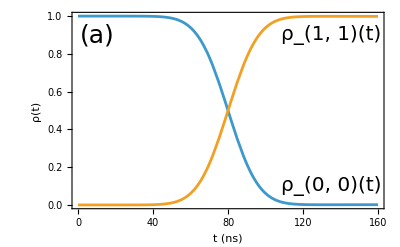

```mathematica
Show[
Plot[{Re[rho[[1,1]]],Re[rho[[2,2]]]},{t,tmin,tmax},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["ρ(t)",Italic,20]}],
Graphics[{
Text[Style["ρ_(1, 1)(t)",20],{135,0.9}],
Text[Style["ρ_(0, 0)(t)",20],{135,0.1}],
Text[Style["(a)",25],{10,0.9}]
}]
]
```

We can also get a notion of the magnitude of the leakages of probability by plotting the density matrix ρ_(3,3) and ρ_(4,4)

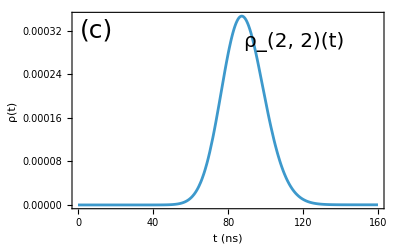

```mathematica
Show[
Plot[Re[rho[[3,3]]],{t,tmin,tmax},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["ρ(t)",Italic,20]}],
Graphics[{
Text[Style["ρ_(2, 2)(t)",20],{115,0.0003}],
Text[Style["(c)",25],{10,0.00032}]
}]
]
```

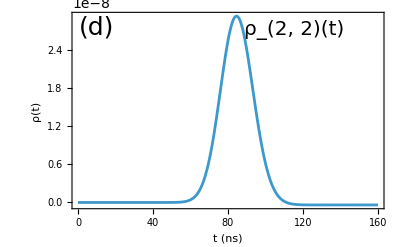

```mathematica
Show[
Plot[Re[rho[[4,4]]],{t,tmin,tmax},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Style["t (ns)",20],Style["ρ(t)",Italic,20]}],
Graphics[{
Text[Style["ρ_(2, 2)(t)",20],{115,2.7 10^-8}],
Text[Style["(d)",25],{10,2.75 10^-8}]
}]
]
```

We can also try other initial configurations, as one in which the second level is initially fully populated.

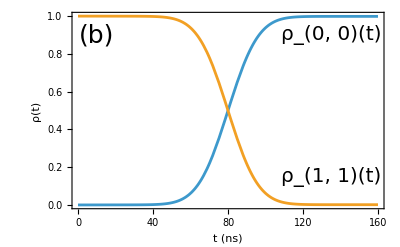

```mathematica
ρ0=ProjectOperatorOntoBasis[SparseArray[{2,2}->1,{m,m}],h];
ρ=fV.X.ρ0;
rho=Normal[ρ.h]/.sol;
Show[
Plot[{Re[rho[[1,1]]],Re[rho[[2,2]]]},{t,tmin,tmax},Axes->False,Frame->True,FrameLabel->{Style["t (ns)",20],Style["ρ(t)",Italic,20]}],
Graphics[{
Text[Style["ρ_(1, 1)(t)",20],{135,0.15}],
Text[Style["ρ_(0, 0)(t)",20],{135,0.9}],
Text[Style["(b)",25],{10,0.9}]
}]
]
```

The preceding results suggest behavior consistent with an X gate. To assess how closely the evolution approximates this gate, we compute the dynamical map projected onto the computational subspace spanned by the two lowest energy levels, |0⟩ and |1⟩. We start by computing the dynamical mat in the Liouville space and evaluate it at t = tmax.

```mathematica
Vmat=Normal[fV.X]/.sol/.{t->tmax};
```

To obtain the dynamical map on the computational subspace spanned by the two lowest energy levels, |0⟩ and |1⟩ we construct a one-qubit operator basis, embed it in the four-level operator space, and project V(t) onto it.

```mathematica
g0=QubitBasis[1];
g=KroneckerProduct[SparseArray[{1,1,1}->1,{1,2,2}],g0];
T=TensorContract[g.Transpose[h],{{2,4}}];
MatrixForm[Chop[T.Vmat.Transpose[T],1 10^-5]]
```

(1. | 0 | 0 | 0
0 | 0.996415 | -0.0000104398 | 0.027867
0.000560942 | 0 | -0.996999 | 0.000492295
0 | 0.027867 | -0.000492492 | -0.997285)

This result can be compared with the actual dynamical map of the gate X.

```mathematica
U = PauliMatrix[1];
TensorContract[(g0.U).Transpose[g0.ConjugateTranspose[U]],{{2,4}}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

This result indicates that the implemented operation approximates an X gate.

## Example 4. Three qubits.

### Three-qubit matrix basis h

In the following example we verify the main relations derived in the paper for the two qubit case.

```mathematica
nq=3;
```

We begin by constructing the one-qubit basis 𝔥_n and its associated structure constant superoperators Z, Z^* and X.

```mathematica
h=QubitBasis[nq];
{b,c}=BCStructureConstantsFromQubits[nq];
z=ZStructureConstantsFromQubits[nq];
zt=Conjugate[z];
x=XBasisFromQubits[nq];
```

The  complex structure-constant superoperators can be visualized with the following line of code.

```mathematica
MatrixForm[z[[3]]]
```

(0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0)

It can be verified that Z and Z^* constitute to independent realizations of the Lie algebra associated with h by showing that the following difference, obtained by subtracting the right-hand side from the left-hand side of Eqs. (69) and (70), vanish identically.

```mathematica
zz=Transpose[z.Transpose[z],{1,3,2,4}];
commu=SparseArray[zz-Transpose[zz]];
PossibleZeroQ[SparseArray[commu+2ⅈ c.z]]
```

SparseArray[…]

```mathematica
ztzt=Transpose[zt.Transpose[zt],{1,3,2,4}];
commu=SparseArray[ztzt-Transpose[ztzt]];
PossibleZeroQ[SparseArray[commu-2ⅈ c.zt]]
```

SparseArray[…]

Similarly we can verify that Z, Z^* commute.

```mathematica
zzt=Transpose[z.ConjugateTranspose[z]];
ztz=Transpose[zt.Transpose[z],{3,1,2,4}];
commu=SparseArray[zzt-ztz];
PossibleZeroQ[commu]
```

SparseArray[…]

The structure of the elements of X can be visualized using the following line of code.

```mathematica
MatrixForm[x[[2,3]]]
```

(0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/8 | 0 | 0 | 0)

For some computations it is convenient to flatten the first two indices of X.

```mathematica
X=Flatten[x,1]
```

SparseArray[<262144>, {4096, 64, 64}]

### Hamiltonian

A convenient system for illustrating the results developed in this work is the transmon qubit. Since the number of quantum levels retained in the model can be chosen arbitrarily, it provides a simple framework for studying the behavior of the algebraic structures introduced above as the Hilbert-space dimension increases. We first define the lowering and rasing operators as well as the jump operators

```mathematica
m=2^nq;
n=2^(2nq);
a=SparseArray[Table[{n+1,n+2}->√(n+1),{n,0,m-2}],m];
at=SparseArray[Table[{n+1,n}->√n,{n,1,m-1}],m];
A=SparseArray[Table[{n+1,n+1,n+2}->√(n+1),{n,0,m-2}],{m-1,m,m}];
At=SparseArray[Table[{n+1,n+2,n+1}->√(n+1),{n,0,m-2}],{m-1,m,m}];
```

The Hamiltonian in the interaction picture, given by Eq. (122) is given by

```mathematica
ψ = Exp[-ⅈ (Δ t +ϕ)]Map[Exp,ⅈ α t (1-Range[m-1])];
ψt=Exp[ⅈ (Δ t +ϕ)]Map[Exp,-ⅈ α t (1-Range[m-1])];
Hi=Ω/2(ψ.A+ψt.At);
Hi//MatrixForm
```

(0 | 1/2 ⅇ^(-ⅈ (t Δ+ϕ)) Ω | 0 | 0 | 0 | 0 | 0 | 0
1/2 ⅇ^(ⅈ (t Δ+ϕ)) Ω | 0 | (ⅇ^(-ⅈ t α-ⅈ (t Δ+ϕ)) Ω)/(√2) | 0 | 0 | 0 | 0 | 0
0 | (ⅇ^(ⅈ t α+ⅈ (t Δ+ϕ)) Ω)/(√2) | 0 | 1/2 √3 ⅇ^(-2 ⅈ t α-ⅈ (t Δ+ϕ)) Ω | 0 | 0 | 0 | 0
0 | 0 | 1/2 √3 ⅇ^(2 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0 | ⅇ^(-3 ⅈ t α-ⅈ (t Δ+ϕ)) Ω | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(3 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0 | 1/2 √5 ⅇ^(-4 ⅈ t α-ⅈ (t Δ+ϕ)) Ω | 0 | 0
0 | 0 | 0 | 0 | 1/2 √5 ⅇ^(4 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0 | √(3/2) ⅇ^(-5 ⅈ t α-ⅈ (t Δ+ϕ)) Ω | 0
0 | 0 | 0 | 0 | 0 | √(3/2) ⅇ^(5 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0 | 1/2 √7 ⅇ^(-6 ⅈ t α-ⅈ (t Δ+ϕ)) Ω
0 | 0 | 0 | 0 | 0 | 0 | 1/2 √7 ⅇ^(6 ⅈ t α+ⅈ (t Δ+ϕ)) Ω | 0)

The Hamiltonian vector is obtained by projecting the Hamiltonian on the elements of the set 𝔥_n through Eq. (23).

```mathematica
H=ExpToTrig[ProjectOperatorOntoBasis[Hi,h]];
MatrixForm[H]
```

(0
(Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]
(Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]
0
0
1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]
-1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]
0
0
1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]
1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]
0
0
(Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]
(Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]
0
0
0
0
0
0
(Ω Cos[3 t α+t Δ+ϕ])/(√2)
-(Ω Sin[3 t α+t Δ+ϕ])/(√2)
0
0
-(Ω Sin[3 t α+t Δ+ϕ])/(√2)
-(Ω Cos[3 t α+t Δ+ϕ])/(√2)
0
0
0
0
0
0
0
0
0
0
(Ω Sin[3 t α+t Δ+ϕ])/(√2)
(Ω Cos[3 t α+t Δ+ϕ])/(√2)
0
0
(Ω Cos[3 t α+t Δ+ϕ])/(√2)
-(Ω Sin[3 t α+t Δ+ϕ])/(√2)
0
0
0
0
0
0
(Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]
(Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]
0
0
1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]
-1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]
0
0
1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]
1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]
0
0
(Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]
(Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]
0)

### Lindbladian

To construct the Lindbladian, we first introduce the corresponding jump operators. In the case of transmons, two decoherence processes are particularly relevant: energy relaxation and pure dephasing. Energy relaxation describes the loss of an excitation from the transmon to its environment and is represented by the Lindblad jump operator J_1=a. This process is characterized by the relaxation time T_1, time or equivalently by the relaxation rate  Γ_1=1/T_1.  Although the corresponding contribution to the Lindbladian is time independent in the Schrödinger picture, it becomes time dependent in the interaction picture used here to express the Hamiltonian. For a harmonic oscillator a simple scalar phase cancels completely, but for the anharmonic transmon the phase contains the number operator n=a^†a, that introduces the time dependency. This time dependency is easily introduced through the phases and decomposing into transition operators the lowering and rising operators

```mathematica
J1=SparseArray[Table[{n,n,n+1}->√n Exp[-ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
J1t=SparseArray[Table[{n,n+1,n}->√n Exp[ⅈ α n t],{n,1,m-1}],{m-1,m,m}];
```

The Lindbladian corresponding to the energy relaxation part is defined by Eq. (38)

```mathematica
γ1=SparseArray[Flatten[Table[{ii,jj}->γ10,{ii,m-1},{jj,m-1}]],{m-1,m-1}];
Γ1=GammaFromgamma[h,γ1,J1,J1t];
MatrixForm[Γ1]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0
0 | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0
0 | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Pure dephasing describes a phenomenon that does not change the energy-level populations but instead, destroys coherence between different energy eigenstates. It is characterized by the jump operator J_2=a^†a

```mathematica
J2 = SparseArray[{at.a}];
J2t = SparseArray[{at.a}];
```

and the pure-dephasing time T_2 or rate Γ_2=4 T_1-2/T_2  which is associated

```mathematica
γ2=SparseArray[{{γ20}}];
Γ2=GammaFromgamma[h,γ2,J2,J2t];
MatrixForm[Γ2]
```

(98 γ20 | 0 | 0 | -14 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -28 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -56 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14 γ20 | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-28 γ20 | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-56 γ20 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The full Lindbladian is therefore

```mathematica
Γ=Γ1+Γ2;
MatrixForm[Γ2]
```

(98 γ20 | 0 | 0 | -14 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -28 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -56 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14 γ20 | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-28 γ20 | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-56 γ20 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Algebraic Method

Having obtained the quantities required to construct the Hamiltonian and Lindbladian contributions to the Liouville superoperator, namely H and Γ, we can proceed to compute Λ using Eq. (60), yielding

```mathematica
Λ=LambdaFromHamiltonianLindbladian[z,H,Γ]
MatrixForm[Λ]
```

SparseArray[…]

(98 γ20+√2 (-7 √2 γ10-70 √2 γ20) | 2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | 2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | -14 γ20+(√2 γ10+14 √2 γ20)/(√2) | 0 | 2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 2 ⅈ √2 (-1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 2 ⅈ √2 (1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | -28 γ20+(3 √2 γ10+28 √2 γ20)/(√2) | 2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | 2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | (-√2 γ10-4 √2 γ20)/(√2) | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | -2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | -2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | -2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | -2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | -56 γ20+(7 √2 γ10+56 √2 γ20)/(√2) | 2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | 2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | (-√2 γ10-8 √2 γ20)/(√2) | 0 | 2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 2 ⅈ √2 (-1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 2 ⅈ √2 (1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | (-√2 γ10-16 √2 γ20)/(√2) | 2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | 2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | -γ10
-2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14 γ20+(√2 γ10+14 √2 γ20)/(√2) | 0 | 0 | 2 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (-1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]+1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-28 γ20+(3 √2 γ10+28 √2 γ20)/(√2) | 0 | 0 | 4 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0
-2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]+1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0
(-√2 γ10-4 √2 γ20)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ Ω Cos[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | -(ⅈ γ10)/4 | -γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 ⅈ Ω Sin[3 t α+t Δ+ϕ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | γ10/4 | -(ⅈ γ10)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/4 | (ⅈ γ10)/4 | 0 | 0 | (ⅈ γ10)/4 | γ10/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-56 γ20+(7 √2 γ10+56 √2 γ20)/(√2) | 0 | 0 | 8 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 γ20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0
-2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)+1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]-1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0
(-√2 γ10-8 √2 γ20)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (-1/2 Ω Sin[t α+t Δ+ϕ]+1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Sin[t α+t Δ+ϕ]-1/2 √3 Ω Sin[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 (1/2 Ω Cos[t α+t Δ+ϕ]-1/2 √3 Ω Cos[5 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | -γ10/2 | (ⅈ γ10)/2 | 0 | 0 | -(ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | (ⅈ γ10)/2 | γ10/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-√2 γ10-16 √2 γ20)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √2 ((Ω Cos[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Cos[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Cos[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Cos[6 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10 | -ⅈ γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ10/2 | -(ⅈ γ10)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ10 | ⅈ γ10 | 0
-2 ⅈ √2 ((Ω Sin[t Δ+ϕ])/(2 √2)-1/2 √(3/2) Ω Sin[2 t α+t Δ+ϕ]-1/2 √(5/2) Ω Sin[4 t α+t Δ+ϕ]+1/2 √(7/2) Ω Sin[6 t α+t Δ+ϕ]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ γ10 | -γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ γ10)/2 | -γ10/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ γ10 | γ10 | 0
-γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The Liouville superoperator is obtained using Eq. (59).

```mathematica
Lam=SparseArray[LiouvilleSOFromLamda[x,Λ]]
```

SparseArray[<1054>, {64, 64}]

### Direct method

The Liouville superoperator is also computed in the same matrix basis for comparison. The two methods are found to yield identical results.

```mathematica
Ldm=SparseArray[LiouvilleSOFromProjection[h,H,Γ]];
```

### Comparison of the algebraic method and the direct method

To compare the Liouville superoperators obtained using the algebraic and direct methods, we subtract one superoperator from the other.

```mathematica
PossibleZeroQ[SparseArray[Lam-Ldm]]
```

SparseArray[…]

### Liouville equation for the dynamical map

To verify that the dynamical differential equations for the coordinate vector, Eq. (112), are equivalent to those derived from the Lindbladian, we directly project the Liouville operator acting on the dynamical map, as given on the right-hand side of Eq. (110), onto the basis X. We then subtract the resulting expression from the right-hand side of Eq. (112), which should yield zero if both formulations are equivalent. First, we define the elements of the dynamical map as in Eq. (107).

```mathematica
V=SparseArray[Array[v[##][t]&,{n,n}]];
```

We calculate the right-hand side of the dynamical differential equations using the algebraically derived Eq. (112).

```mathematica
DiffEqsAlgebraicMethod=SparseArray[Flatten[V].Flatten[Transpose[SparseArray[1/4 zt.Λ.z],{1,3,2,4}],1]]
```

SparseArray[<4096>, {64, 64}]

Here, we project the Liouville operator obtained through the direct method, acting on the dynamical map as given on the right-hand side of Eq. (110), onto the basis X.

```mathematica
DiffEqsDirectMethod=TensorContract[Transpose[V].TensorContract[x.Transpose[x,{2,3,1,4}].Ldm,{{3,6}}],{{1,2}}]
```

SparseArray[…]

Finally, we compare the results obtained by both methods.

```mathematica
PossibleZeroQ[SparseArray[DiffEqsDirectMethod-DiffEqsAlgebraicMethod]]
```

SparseArray[…]